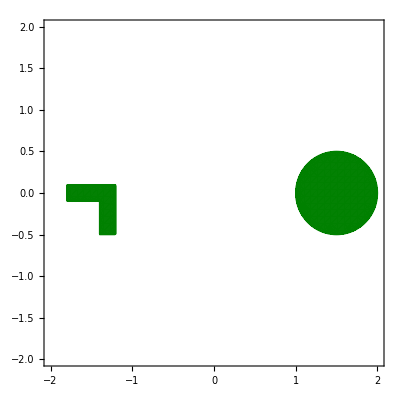

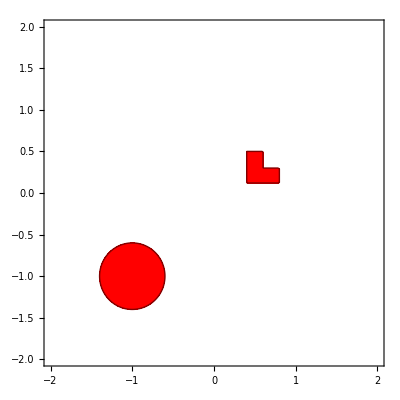

-15.1048+22.0165 x+14.4348 x^2-14.1033 x^3-18.677 x^4-5.57511 x^5+40.6922 y+72.0145 x y-10.8632 x^2 y-35.0285 x^3 y+2.75372 x^4 y-85.8866 y^2-23.7842 x y^2+44.2641 x^2 y^2+0.783265 x^3 y^2+50.0719 y^3+24.5623 x y^3+45.4087 x^2 y^3+277.559 y^4-3.53978 x y^4-169.394 y^5

-9.25124+13.1397 x+9.68381 x^2-3.88915 x^3-8.47 x^4-2.99796 x^5+40.5822 y+40.5272 x y-16.3614 x^2 y-34.7509 x^3 y-0.780589 x^4 y-128.735 y^2-28.1474 x y^2+35.975 x^2 y^2+2.70694 x^3 y^2+66.3317 y^3+12.5372 x y^3-13.2088 x^2 y^3+372.977 y^4+43.4094 x y^4-274.863 y^5

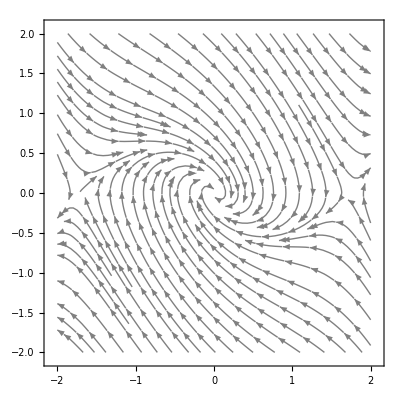

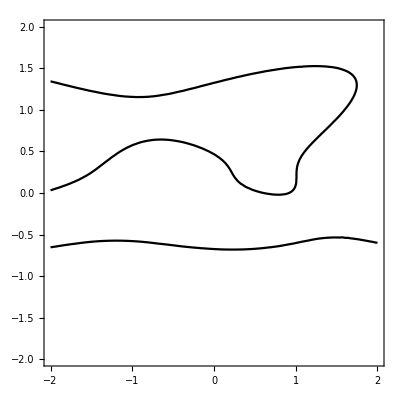

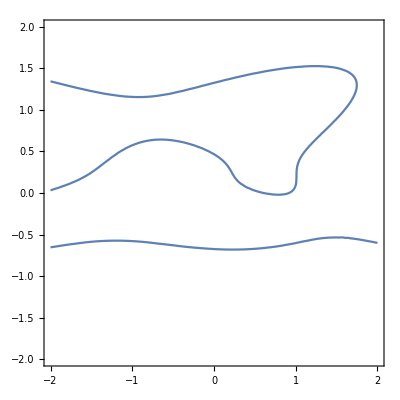

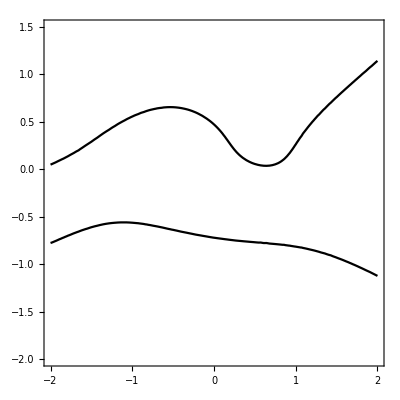

-Graphics-

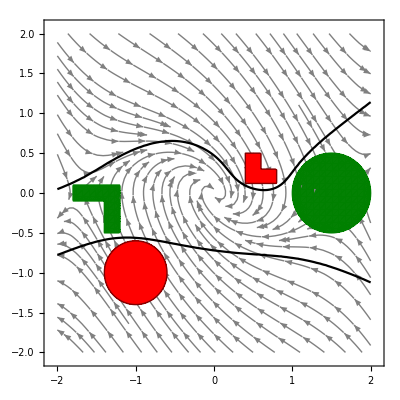

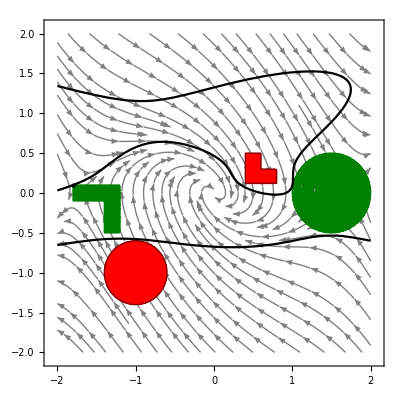

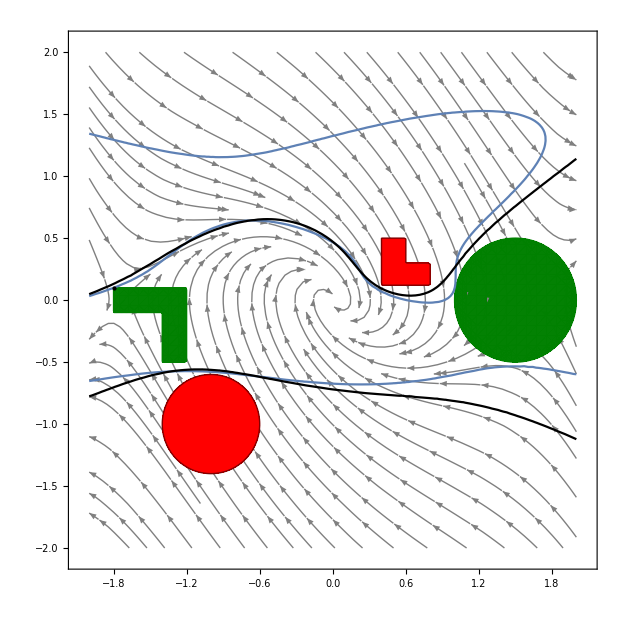

```mathematica
phi=RegionPlot[(x≥-1.8&&x≤-1.2&&y≥-0.1&&y≤0.1)||(x-1.5)^2+y^2≤0.25||(x≥-1.4&&x≤-1.2&&y≥-0.5&&y≤0.1),{x,-2,2},{y,-2,2},PlotPoints->50,BoundaryStyle->Directive[RGBColor[0,0.5,0], Thin],PlotStyle->Directive[RGBColor[0,0.5,0],Opacity[0.99]]]
psi1=RegionPlot[(x≥0.4&&x≤0.6&&y≥0.12&&y≤0.5)||(x+1)^2+(y+1)^2≤0.16||(x≥0.4&&x≤0.8&&y≥0.12&&y≤0.3),{x,-2,2},{y,-2,2},PlotPoints->70,PlotStyle->Directive[Red],BoundaryStyle->Directive[RGBColor[0.5,0,0], Thin]]
V=-5.575105681595*x^5+2.75371876561447*x^4*y-18.6770133119871*x^4+0.783265458260983*x^3*y^2-35.0285399354595*x^3*y-14.1033375900034*x^3+45.4086683641139*x^2*y^3+44.2641235060537*x^2*y^2-10.8631624877137*x^2*y+14.4347843279824*x^2-3.53978162282468*x*y^4+24.5623051318757*x*y^3-23.7842239132673*x*y^2+72.014460096173*x*y+22.0164924966179*x-169.394267740555*y^5+277.558525699016*y^4+50.0719216616459*y^3-85.8865621406248*y^2+40.6921625229521*y-15.1047891792979

V2 = -2.99795535112848*x^5-0.780589364605559*x^4*y-8.47000328547583*x^4+2.70694457574967*x^3*y^2-34.7509043383118*x^3*y-3.88915121656548*x^3-13.2088359765202*x^2*y^3+35.9750088105682*x^2*y^2-16.3614486138458*x^2*y+9.68381161774933*x^2+43.4093544529448*x*y^4+12.5372104288293*x*y^3-28.1473819162028*x*y^2+40.5271734975715*x*y+13.1396567851088*x-274.862649555301*y^5+372.977035949673*y^4+66.3316971820201*y^3-128.734729056483*y^2+40.5821795096257*y-9.2512402696589

Vector=StreamPlot[{y,-x-y+x^3/3},{x,-2,2},{y,-2,2},StreamStyle->Gray]

domain1 = ContourPlot[V2==0,{x,-2,2},{y,-2,2},ContourStyle->Directive[Black]]
domain3= ContourPlot[V2==0,{x,-2,2},{y,-2,2},ContourStyle->Directive[blue]]
domain2 = ContourPlot[V==0,{x,-2,2},{y,-2,1.5},ContourStyle->Directive[Black]]
counter=Graphics[{PointSize[Medium],Point[{{-1.7998255,0.0996077}},VertexColors->{Red}]}]
Show[Vector,phi,psi1,domain2]
Show[Vector,phi,psi1,domain1,counter]
Show[Vector,phi,psi1,domain3,domain2,counter]
```

```mathematica
|
```